```mathematica
$Assumptions={r>0,r0>0,u>0,s>0,h>0,a>0,a>s, r<a, r0<a, r>s, r0>s, D>0,t>0,n∈Integers,n>0,theta≥0,theta≤π}
```

{r>0,r0>0,u>0,s>0,h>0,a>0,a>s,r<a,r0<a,r>s,r0>s,D>0,t>0,n∈Integers,n>0,theta≥0,theta≤π}

```mathematica
transsbessel:={BesselJ[n_+2 nn_(1/2),z_]->SphericalBesselJ[n+nn-1/2,z] / Sqrt[Pi/(2 z)],BesselY[n_+2 nn_ (1/2),z_]->SphericalBesselY[n+nn-1/2,z] / Sqrt[Pi / (2z)]}
```

```mathematica
solnBJY:=(1+2 n)(π u^2 (((n-h s) BesselJ[1/2+n,s u] -s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r u]+BesselJ[1/2+n,r u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])) (((n-h s) BesselJ[1/2+n,s u] -s u BesselJ[3/2+n,s u] )BesselY[1/2+n,r0 u]+BesselJ[1/2+n,r0 u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])))/(8 √r √r0( n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)))
```

```mathematica
solnBJY/. n->0 // Simplify
```

((s u Cos[(r-s) u]+(1+h s) Sin[(r-s) u]) (s u Cos[(r0-s) u]+(1+h s) Sin[(r0-s) u]))/(2 π r r0 (-s^2 (h+h^2 s+s u^2)+a (1+2 h s+h^2 s^2+s^2 u^2)))

```mathematica
falpha[a_] = ((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u] + BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])
```

((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u]+BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])

```mathematica
transfa ={ ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]) -> - ((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u] / BesselJ[1/2+n,a u]}
```

{(-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]→((-(n-h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u])/BesselJ[1/2+n,a u]}

```mathematica
falpha[a]  == 0/. transfa // Simplify
```

True

```mathematica
falpha[a] /. transsbessel  // Simplify
```

1/π 2 √(a s) u ((n-h s) SphericalBesselJ[n,s u] SphericalBesselY[n,a u]-s u SphericalBesselJ[1+n,s u] SphericalBesselY[n,a u]+SphericalBesselJ[n,a u] ((-n+h s) SphericalBesselY[n,s u]+s u SphericalBesselY[1+n,s u]))

```mathematica
falpha0 = FullSimplify[falpha[a] /. n->0, Assumptions->{a>0,u>0,s>0}]
```

-(2 (s u Cos[(a-s) u]+(1+h s) Sin[(a-s) u]))/(π √(a s) u)

```mathematica
E1 = n + n^2 - s( h + h^2 s + s u^2) + (( (-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2 + ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2 )/ ( BesselY[1/2+n,a u]^2+BesselJ[1/2+n,a u]^2)
```

n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)

```mathematica
E2 = n + n^2 - s( h + h^2 s + s u^2) + ( (-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2  / BesselJ[1/2+n,a u]^2
```

n+n^2-s (h+h^2 s+s u^2)+((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2/BesselJ[1/2+n,a u]^2

```mathematica
pni = ((1+2 n) π u^2)/(8 √(r r0)) falpha[r] falpha[r0] / E2 // Simplify
```

((1+2 n) π u^2 (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r u]+BesselJ[1/2+n,r u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])) (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r0 u]+BesselJ[1/2+n,r0 u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])))/(8 √(r r0) (n+n^2-s (h+h^2 s+s u^2)+((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2/BesselJ[1/2+n,a u]^2))

```mathematica
pni
```

((1+2 n) π u^2 (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r u]+BesselJ[1/2+n,r u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])) (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r0 u]+BesselJ[1/2+n,r0 u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])))/(8 √(r r0) (n+n^2-s (h+h^2 s+s u^2)+((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2/BesselJ[1/2+n,a u]^2))

```mathematica
pni1 = pni /. transfa // FullSimplify
```

((1+2 n) π u^2 ((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2 (BesselJ[1/2+n,r u] BesselY[1/2+n,a u]-BesselJ[1/2+n,a u] BesselY[1/2+n,r u]) (BesselJ[1/2+n,r0 u] BesselY[1/2+n,a u]-BesselJ[1/2+n,a u] BesselY[1/2+n,r0 u]))/(8 √(r r0) ((n+n^2-s (h+h^2 s+s u^2)) BesselJ[1/2+n,a u]^2+((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u])^2))

```mathematica
falpha[a]
```

((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u]+BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])

```mathematica
pni1 == solnBJY /. transfa // Simplify
```

True

```mathematica
pni1 /. transsbessel // FullSimplify
```

(a (1+2 n) s u^4 ((-n+h s) SphericalBesselJ[n,s u]+s u SphericalBesselJ[1+n,s u])^2 (-SphericalBesselJ[n,r u] SphericalBesselY[n,a u]+SphericalBesselJ[n,a u] SphericalBesselY[n,r u]) (-SphericalBesselJ[n,r0 u] SphericalBesselY[n,a u]+SphericalBesselJ[n,a u] SphericalBesselY[n,r0 u]))/(2 π (a (n+n^2-s (h+h^2 s+s u^2)) SphericalBesselJ[n,a u]^2+s ((-n+h s) SphericalBesselJ[n,s u]+s u SphericalBesselJ[1+n,s u])^2))

```mathematica
transbesselrecur ={ BesselJ[-1/2+n,a u] -> ((2 n + 1 ) / (a u ) )BesselJ[1/2+n,a u]  - BesselJ[3/2+n,a u], BesselY[-1/2+n,a u] -> ((2 n + 1 ) / (a u ) )BesselY[1/2+n,a u]  - BesselY[3/2+n,a u]}
```

{BesselJ[-1/2+n,a u]→((1+2 n) BesselJ[1/2+n,a u])/(a u)-BesselJ[3/2+n,a u],BesselY[-1/2+n,a u]→((1+2 n) BesselY[1/2+n,a u])/(a u)-BesselY[3/2+n,a u]}

```mathematica
Dsolnata = D D[pni1,r]/.{r->a} /. transbesselrecur /. transfa// FullSimplify
```

(D (1+2 n) r0 u^2 ((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2 (-BesselJ[1/2+n,r0 u] BesselY[1/2+n,a u]+BesselJ[1/2+n,a u] BesselY[1/2+n,r0 u]))/(4 (a r0)^(3/2) ((n+n^2-s (h+h^2 s+s u^2)) BesselJ[1/2+n,a u]^2+((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u])^2))

```mathematica
Dsolnata == D D[solnBJY,r]/.{r->a} /. transbesselrecur/. transfa// Simplify
```

True

```mathematica
Dsolnata //. transsbessel  // Simplify
```

(D (1+2 n) s u^3 ((n-h s) SphericalBesselJ[n,s u]-s u SphericalBesselJ[1+n,s u])^2 (-SphericalBesselJ[n,r0 u] SphericalBesselY[n,a u]+SphericalBesselJ[n,a u] SphericalBesselY[n,r0 u]))/(2 a π (a (n+n^2-s (h+h^2 s+s u^2)) SphericalBesselJ[n,a u]^2+s ((n-h s) SphericalBesselJ[n,s u]-s u SphericalBesselJ[1+n,s u])^2))

Integrating LegendreP[n,Cos[theta]];  integration by substitution.  Note the Jacobian Sin[theta].

```mathematica
intlgnd = Integrate[Sin[ArcCos[x]] LegendreP[n,x] (1/(-Sin[ArcCos[x]])), {x,Cos[0],Cos[theta]}] // FullSimplify
```

(LegendreP[-1+n,Cos[theta]]-LegendreP[1+n,Cos[theta]])/(1+2 n)

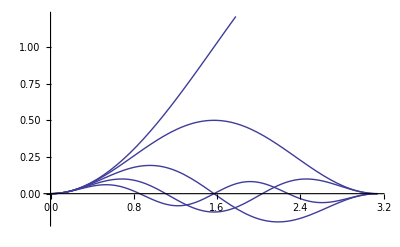

```mathematica
Plot[intlgnd/.n->{0,1,2,3,4},{theta,0,Pi}]
```

verify

```mathematica
D[intlgnd,theta] == Sin[theta] LegendreP[n,Cos[theta]]// FullSimplify
```

n Cot[theta] LegendreP[-1+n,Cos[theta]]+LegendreP[n,Cos[theta]] (-n Cos[2 theta] Csc[theta]+Sin[theta])==(2+n) (Cot[theta] LegendreP[1+n,Cos[theta]]-Csc[theta] LegendreP[2+n,Cos[theta]])

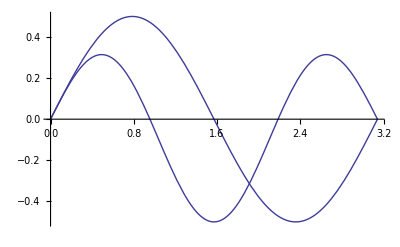

```mathematica
Plot[Sin[theta] LegendreP[n,Cos[theta]]/. n->{1,2},{theta,0,Pi}]
```

```mathematica
Limit[falpha[a,s,u] , h->Infinity]
```

DirectedInfinity[-s BesselJ[1/2+n,s u] BesselY[1/2+n,a u]+s BesselJ[1/2+n,a u] BesselY[1/2+n,s u]]

Special case; r0 == sigma

```mathematica
solnBJY /. r0 -> s // FullSimplify
```

$Aborted

```mathematica
Limit[solnBJY/. n->0,s->0]  //Simplify
```

(Sin[r u] Sin[r0 u])/(2 a π r r0)

((1+2 n) π u^2 (-n BesselJ[1/2+n,r u] BesselY[1/2+n,0]+n BesselJ[1/2+n,0] BesselY[1/2+n,r u]) (-n BesselJ[1/2+n,r0 u] BesselY[1/2+n,0]+n BesselJ[1/2+n,0] BesselY[1/2+n,r0 u]))/(8 √r √r0 (n+n^2+(n^2 BesselJ[1/2+n,0]^2+n^2 BesselY[1/2+n,0]^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)))